Last modified on: Friday, June 29, 2018 at 21:04

Author Info

Faizon

Zaman

SUNY Oswego

Poster Session Content

Wolfram-Twine Bridge

The goal is to build an Import/Export system between Twine and the Wolfram Language. Twine is browser-based software used to make interactive stories and text-based games. A Twine story or game consists of a network of passages and macros that can change the state of variables or other story elements. Graphs and Associations will be used to represent Twine Stories in the Wolfram Language. The primary goal is importing the Twine Story HTML file into the form of a Wolfram Language Graph and Association, and exporting an Association form to the Twine HTML format.

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

-Graphics-

Import support for Twine Stories made using the Harlowe markup language. The importer can generate a Graph and Association form for any html file with the Twine  format. The Twine Link syntax is supported as long as it is not in a macro (commands for changing states of story elements). Using the Association form,  a Twine Summary can be generated to explore the passages via a Clickable Graph. Association Forms  can be exported to the Twine HTML format. A folder is generated in the notebook directory where the story will be stored. These can then be imported into Twine.

The Harlowe markup language has support for macros: commands that can change story elements (appearance, flow, state etc.). Among other types, there are conditional, printing, data and output macros. Some macros include Links to other passages, which I can’t support yet as they are effectively hidden from my parser. The next step is to gradually implement these macros and continually increase the number of stories I am testing on. Any errors or unsupported features can be approached in this step-wise fashion.

Note: Everything above this bar is your poster.Make sure it fits on a single page. "Preview Poster"

End of School Presentation Content

In addition to the poster content, include other content to present at the 2 minute presentation for end of school. Use the buttons below to add more sections."Add Header""Add Text""Add Code or Image"

Association Form

Here is an Association form of a Twine Story

Section Header

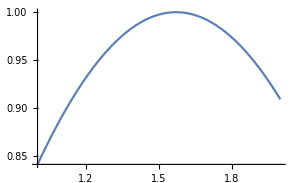
Plot[Sin[x],{x,1,2}]
-Graphics-

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

#### Main Results in Detail

Import support for Twine Stories made using the Harlowe markup language. Harwlowe is the default markup language that the Twine Editor uses (others: sugarcane, sugarcube). The first thing to do in representing a graph or network is defining what the nodes and edges are. In the Twine case passages are nodes and  connections between passages are edges. All of these edges are directed, going from the passage the link is contained in to the passage specified in the link. To specify a link, the passage to link to is placed within a pair of Double Square Brackets: [[LinkName]]. There are also hidden links with three ways to specify them: [[Go Here-> Door Number 3]] , [[Door Number 3<-Go Here]], [[Go Here|Door Number 3]]. The user will see the text “Go Here” but will end up at the passage named “Door Number 3”. This syntax is supported as long as it is not in a macro (commands for changing states of story elements). 

There was Initial trouble importing the Twine files, though If I Imported with the XMLObject format spec it would work. The problem then became that the XML I got back was formatted incorrectly. A Body tag was separating passage contents from their parent node. Riccardo wrote an XML parser that fixed the issue. 

| IMPORTER |

The import procedure has to do a few things: Extract elements from an html document and generate a graph and association. First, the html file is imported as a string. Some Published Twine Files have non story/passage information. It is ignored by using StringCases to find the content that starts with open tag <tw-storydata> and ends with the closing tag </tw-storydata>. This result is then parsed by Riccardo’s parser. From the generated XML content the root node and its name, as well as the passages, are extracted using Cases. Then an Association is created between passage names and their respective content to be used in tooltips in the generated graph via AssociationThread while also removing the link syntax. AssociationTo is then used to add the rootNode to that association. Then a list of edges is created between a passage and any links contained in its content. The DIrected Edge from the root node to the first passage is then prepended to that list. A graph is generated with these edges. Tooltips were then iteratively wrapped around the vertices using Table. A final graph was constructed using the Tooltip vertices and the list of all the edges.  Then the output Association Form is generated. First, using AssociationThread just as before, the passage names and passage contents enter a key-value grouping, except link syntax is retained. Then the root node’s name is given as the key to the Association of passages. Finally, a list containing the graph and the association is returned.

| EXPORTER |

The exporter takes in an Association form of a story. The form is:
	
	 		<| “StoryTitle” → <| “PassageName” → ”PassageContent” ...|>

One of the metadata options for a Twine Story passage is the position of the passage, because in the Twine Editor one can drag passages around in a workspace. A simple way to get the vertices is just use the vertex coordinates form a graph representation of the story, this can be don with GraphEmbedding. The twineSummary function will be discussed next, but it can be used to return just the clickable graph. To get the vertex coordinates we can do the following:

			GraphEmbedding[twineSummary[<| “story” → ...|>, “Graph”]]

This is great, except that these points are not scaled correctly for the Twine Workspace. The right way to scale these points are still being experimented with. The current method is to Rescale the points (range: -1, 1) to values between 0 and 250. 

The next thing to do is embed data into a string that can be exported to HTML. StringTemplate was used for this. The first StringTemplate contains some metadata for the Story and a template slot is used for the story title:

			StringTemplate[“<tw-storydata name=\“`storyTitle`\” 
				...”][<| “storyTitle” → First[Keys[<| “story” → ...|>]]|>]
			
To embed the passages more StringTemplates are generated. One for each passage in the passage association. This is done using Table.

passageAssoc = First[Values[<| “story” → ...|>]];
assocLength = Length[assocLength];
Table[StringTemplate[“<tw-passagedata pid=\“`pid`\” name=\“`passagename`\”
		... ”][<| “pid” → index, “passagename” → Keys[passageAssoc]⟦index⟧ ... |>]
				, {1, assocLength, 1};
				]
Then I join the header, passage template and the closing tag for the story and export this as an HTML Fragment.

| SUMMARIZER |

The summarizer has three functions; Summary which returns a GraphicsRow containing the Clickable Graph and Dynamic passage viewer,  Graph which returns the clickable graph by itself, and Export which exports the story in HTML format to a folder called TwineStories.

The Dynamic Viewer allows buttons on the graph to modify what the viewer displays. The dynamic viewer displays the content stored in the symbol activePassage. activePassage is initialized with the story name. ::: Then the edges for the graph are created ::: The passages are then cleaned to remove markdown syntax

Using the Association form,  a Twine Summary can be generated to explore the passages via a Clickable Graph. Association Forms  can be exported to the Twine HTML format. A folder is generated in the notebook directory where the story will be stored. These can then be imported into Twine.

#### Code

GitHub Repo

#### Notes

The initial goal of the project is to develop an import export system between the Wolfram Language and Twine. What were the implementation tasks for this project?

First : Figure out the structure of the Twine Story:
	I found that there was a particular and simple structure representing the story.
		- <tw-storydata> <tw-passagedata></tw-passaagedata> … </tw-storydata>
		The builtin parser was having troube parsing the Twine HTML file correctly, Riccardo wrote a parser that nested the elements correctly. From there I was able to pick apart the neccessary elements and generate a graph and association from the story.

Another thingI did was implement an exporter and summarizer. The summarizer takes in the association form and can show a button graph with a dynamic passage viewer that changes by button clicks, or just the graph, or just Export the file. The summarizer exports to the TwineStories folder in the Notebook Directory

The twinExport function allows one to specify directly / explicitly where to save the files via a path string.

These are the basic results. I will look through my project files and notes that I wrote and add them to the Project notebook. I started attempting implementation of macros.

Do I Need the Intermediate File—Twine saves intermediate files to the browser’s local storage, can’t access this
Exploration—Twine stories are about exploration. Do we want the Graph representation in WL to be explorable?
If yes, it won’t be like the exploration in Twine itself. It will be a computable exploration. Look at Graph functions for some insight.

–	Just focus on Harlowe markup support (which is the default markup language for Twine)

Initially, the Exported HTML did not work in Twine because I neglected the metadata of tw-storydata and tw-passagedata tags. After I hardcoded the metadata Exports worked. The question with this is how to keep the metadata up to date.

Not including metadata caused The Twine app to hang, so I had to re-download it

#### Conclusions in Detail

It is relatively easy to work with HTML. It may have been a bug that nested the tags improperly. Riccardo’s code fixed that problem so I could import the html correctly.  
I learned how to represent Twine’s particular HTML structure in Association and Graph forms. I learned how to extract and replace String Patterns. I learned how to Generate Graphs and replace their vertices with buttons.


There was a lot of Extraction from Data Structures, Replacing and Isolating String Patterns

How well did I succeed in the original goal?

#### All Visualizations

#### Data Sources Links/References

Zip File (Contains the html) | Depths of Sarcasm

#### Future Directions

If all goes well, Machine generated stories generated by the Wolfram Language can be exported as twine stories and uploaded to the internet, (or perhaps any graph). Whether the Graph in WL can be explored in a Twine-Like way via the notebook, is yet to be determined.
The Harlowe markup language has support for macros: commands that can change story elements (appearance, flow, state etc.). Among other types, there are conditional, printing, data and output macros. Some macros include Links to other passages, which I can’t support yet as they are effectively hidden from my parser. The next step is to gradually implement these macros and continually increase the number of stories I am testing on. For each parsing or macro error in a story, I can implement a fix.

Working with opensource software — this means I’m going to have to maintain this functionality as the Harlowe markup language changes

Passage Position on Export

Construct a Grammar (DCG?) that can parse a Twine Story into Appropriate Wolfram Language Expressions

#### Background Info Links/References

Twine Reference

#### Keywords

Provide keywords as items

< keyword 1 >

< keyword 2 >

#### Other information